```mathematica
SetDirectory[NotebookDirectory[]]
data=Import["/Users/zackarywindham/Research/Post-Minkowski/PMdata.csv"]
{x1,y1,z1,px1,py1,pz1,x2,y2,z2,px2,py2,pz2,x3,y3,z3,px3,py3,pz3,hamil}=data;
```

/Users/zackarywindham/Research/Post-Minkowski

{{-1950.,-1949.86,-1949.73,-1949.61,-1949.5,-1949.39,-1949.3,1187,-1823.08,-1822.21,-1821.34,-1820.48,-1819.61,-1818.74,-1817.88},17,{1}}
 |  |  |  |

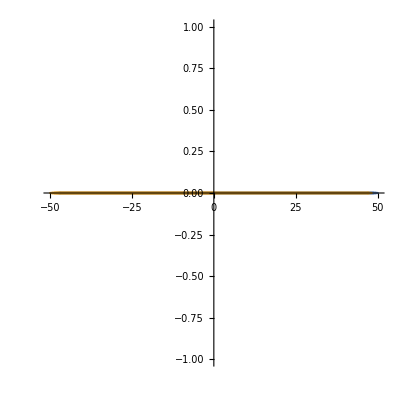

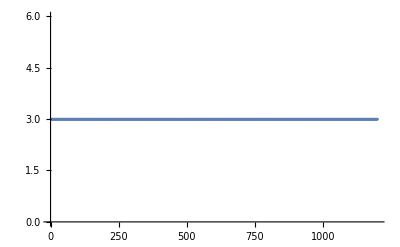

```mathematica
ListPlot[{Transpose[{y1,z1}],Transpose[{y2,z2}]},AspectRatio->1,Joined->True]
ListPlot[Delete[hamil,1]]
```